# Les polynômes orthogonales

## Formule de Rodrigues - Les polynômes de Jacobi P_n^(ν,μ)(x) - Les polynômes de Chebyshev I T_n(x)

```mathematica
Clear["Global`*"]
```

Les polynômes de Jacobi, notés P_n^(ν,μ)(x)forment une suite de polynômes, P_0^(ν,μ)(x),P_1^(ν,μ)(x),P_2^(ν,μ)(x),...,P_np^(ν,μ)(x). Dans cette notation np est le nombre des polynômes qu'on veut les dériver et ν>-1 est un nombre réel .

```mathematica
np:=3
```

```mathematica
ν:=-1/2
```

```mathematica
μ:=-1/2
```

## Formule de Rodrigues

Les polynômes de Chebyshev I peut être définie par la formule de Rodrigues :

```mathematica
P[n_,ν_,μ_,x_]:=1/(K[n] w[x])D[(w[x] s[x]^n), {x,n}]
```

### Initiation

```mathematica
table:=({{"Un polynôme de degrée 0, 1, ou 2", "s[x]", s[x_]=1-x^2}, {"Fonction poids", "w[x]", w[x_]=(1-x)^ν(1+x)^μ}, {"Limite gauche d'intervalle d'orthogonalité", "a", a=-1}, {"Limite droite d'intervalle d'orthogonalité", "b", b=+1}, {"Multiplicateur de standardisation", "K_n", K[n_]=(-1)^n((2n)!)/(2^n n!)}, {"Définition du nombre d'Euler", "e", e=ⅇ}, {"Carré de la norme", "H_n", H[n_]=Piecewise[{{π, n==0}, {π/2, n>0}}]}, {"λ_n dans  l' équation différntiel ", "λ_n", λ[n_]=n(K[1]D[P[1,ν,μ,x], {x,1}]+1/2(n-1)D[s[x], {x,2}])}})
```

### Tableau

```mathematica
Grid[table//FullSimplify,Frame->All]
```

Un polynôme de degrée 0, 1, ou 2 | s[x] | 1-x^2
Fonction poids | w[x] | 1/(√(1-x^2))
Limite gauche d'intervalle d'orthogonalité | a | -1
Limite droite d'intervalle d'orthogonalité | b | 1
Multiplicateur de standardisation | K_n | ((-1/2)^n (2 n)!)/(n!)
Définition du nombre d'Euler | e | ⅇ
Carré de la norme | H_n | Piecewise[{{π, n==0}, {π/2, n>0}, {0, True}}]
λ_n dans  l' équation différntiel  | λ_n | -n^2

## Les polynômes

```mathematica
TableForm[Table[{n,P[n,ν,μ,x]},{n,0,np}]//Simplify,TableAlignments->Left,TableSpacing->{3,5},TableHeadings->{None,{"n","P[n,ν,μ,x]"}}]
```

n | P[n,ν,μ,x]
0 | 1
1 | x
2 | -1+2 x^2
3 | x (-3+4 x^2)

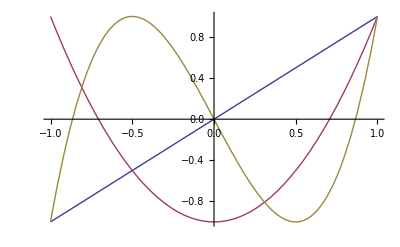

```mathematica
Plot[Evaluate[Table[P[n,ν,μ,x],{n,np}]],{x,-1,1}]
```

## Orthogonalité

```mathematica
Table[∫_a^b w[x]P[n,ν,μ,x]P[n',ν,μ,x]ⅆx,{n,0,np},{n',0,np}]//TableForm
```

π | 0 | 0 | 0
0 | π/2 | 0 | 0
0 | 0 | π/2 | 0
0 | 0 | 0 | π/2

```mathematica
Table[H[n] KroneckerDelta[n,n'],{n,0,np},{n',0,np}]//TableForm
```

π | 0 | 0 | 0
0 | π/2 | 0 | 0
0 | 0 | π/2 | 0
0 | 0 | 0 | π/2

## Normalization

```mathematica
P̃[n_,ν_,μ_,x_]:=P[n,ν,μ,x]/(√H[n])
```

```mathematica
TableForm[Table[{n,P̃[n,ν,μ,x]},{n,0,np}]//Simplify,TableAlignments->Left,TableSpacing->{3,5},TableHeadings->{None,{"n","P̃[n,ν,μ,x]"}}]
```

n | P̃[n,ν,μ,x]
0 | 1/(√π)
1 | √(2/π) x
2 | √(2/π) (-1+2 x^2)
3 | √(2/π) x (-3+4 x^2)

## Orthonormalité

```mathematica
Table[∫_a^b w[x]P̃[n,ν,μ,x]P̃[n',ν,μ,x]ⅆx,{n,0,np},{n',0,np}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

```mathematica
Table[KroneckerDelta[n,n'],{n,0,np},{n',0,np}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

## EDP

Le n - ième polynôme de Laguerre satisfait l' équation différentielle suivante :

```mathematica
EDP=(D[(w[x] s[x]D[u[x], x]), x]-λ[n] w[x]u[x])/w[x]==0//FullSimplify
```

n^2 u[x]+u''[x]==x (u'[x]+x u''[x])

```mathematica
DSolve[EDP,u[x],x]
```

{{u[x]→C[1] Cosh[n Log[x+√(-1+x^2)]]+ⅈ C[2] Sinh[n Log[x+√(-1+x^2)]]}}

```mathematica
TableForm[Table[{n,P[n,ν,μ,x],JacobiP[n,ν,μ,x],(n!√π)/Gamma[n+1/2] JacobiP[n,ν,μ,x],ChebyshevT[n,x]},{n,0,np}]//Simplify,TableSpacing->{3,2},TableHeadings->{None,{"n","P[n,ν,μ,x]","JacobiP[n,ν,μ,x]","(n! SqrtBox[π])/Gamma[n + FractionBox[1, 2]]JacobiP[n,ν,μ,x]","ChebyshevT[n,x]"}}]
```

n | P[n,ν,μ,x] | JacobiP[n,ν,μ,x] | (n! SqrtBox[π])/Gamma[n + FractionBox[1, 2]]JacobiP[n,ν,μ,x] | ChebyshevT[n,x]
0 | 1 | 1 | 1 | 1
1 | x | x/2 | x | x
2 | -1+2 x^2 | 3/8 (-1+2 x^2) | -1+2 x^2 | -1+2 x^2
3 | x (-3+4 x^2) | 5/16 x (-3+4 x^2) | x (-3+4 x^2) | x (-3+4 x^2)